```mathematica
al[s_]:=-2Pi^(s/2)/(s(1-s)Gamma[s/2])
alo[s_]:=-1/((1/2)s(1-s)Pi^(-s/2)Gamma[s/2])
al2[s_]:=-((1/2)s(1-s)Pi^(-s/2)Gamma[s/2])
ssosub[n_,s_]:=((1-s)n^s)/(1/(1/2 (1-s)π^(-(1-s)/2) Gamma[(1-s)/2])n^(1-s)-1/(1/2 s π^(-s/2) Gamma[s/2])n^s)HarmonicNumber[n,s]
ssosub2[n_,s_]:=((1-s)n^s)/((1-s)al[s]n^s-s al[1-s]n^(1-s))HarmonicNumber[n,s]
ssosub3[n_,s_]:=1/(al[s]-al[1-s]s/(1-s) n^(1-2s))HarmonicNumber[n,s]
sso10c[n_,s_]:=ssosub3[n,s]+ssosub3[n,1-s]
ssosub4[n_,s_]:=((1-s)n^s)/((1-s)n^s-s n^(1-s))HarmonicNumber[n,s]
sso10d[n_,s_]:=ssosub4[n,s]+ssosub4[n,1-s]
zetc[n_,s_]:=sso10c[n,s]al[s]
```

```mathematica
sso10c[100000,.5+I]
```

0.483321+0. ⅈ

```mathematica
Zeta[.3+I]al2[.3+I]
```

0.486188-0.00450044 ⅈ

```mathematica
sso10c[1000000,.3+I]al[.3+I]
```

0.0581739-0.591581 ⅈ

```mathematica
Zeta[.3+I]
```

0.0581511-0.591547 ⅈ

```mathematica
zetc[100000,.3+I]
```

0.0579454-0.591517 ⅈ

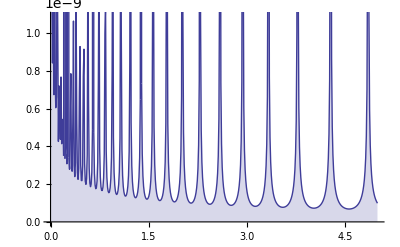

```mathematica
DiscretePlot[Abs@sso10c[n,N@ZetaZero@3],{n,1,50000000,100000}]
```

```mathematica
sso10d[100000000000000000000000000,N@ZetaZero@1+.1I+.06]
```

0.037632+0.0828781 ⅈ

```mathematica
Zeta[N@ZetaZero@1+.1I+.06]
```

0.0377431+0.082786 ⅈ

```mathematica
alo[s]
```

-(2 π^(s/2))/((1-s) s Gamma[s/2])

```mathematica
alo[1-s]
```

-(2 π^((1-s)/2))/((1-s) s Gamma[(1-s)/2])

```mathematica
FullSimplify@alo[1/2+s]
```

(2 π^(1/4+s/2))/((-1+2 s) Gamma[5/4+s/2])

```mathematica
FullSimplify@alo[1/2-s]
```

-(2 π^(1/4-s/2))/((1+2 s) Gamma[5/4-s/2])

```mathematica
alo[s]
```

-(2 π^(s/2))/((1-s) s Gamma[s/2])

```mathematica
alo[1-s]
```

-(2 π^((1-s)/2))/((1-s) s Gamma[(1-s)/2])

```mathematica
po[n_,s_,t_]:=Zeta[s,n+1]((s-1)n^(s-1+t))
po2[n_,s_,t_]:=HarmonicNumber[n,s]((s-1)n^(s-1+t))-HarmonicNumber[n,1-s]((-s)n^(-s+t))
```

```mathematica
po2[1000000000,N@ZetaZero@16,1]
```

0.+67.0797 ⅈ

```mathematica
1.0000000035000012
```

```mathematica
ts[n_,s_,x_]:= (1-s)n^(s-1)Zeta[s,n+1] - (1-s-x)n^(s-1+x)Zeta[s+x,n+1]
tsa[n_,s_,x_]:= (1-s)n^(s-1)(Zeta[s]-HarmonicNumber[n,s]) - (1-s-x)n^(s-1+x)(Zeta[s+x]-HarmonicNumber[n,s+x])
tsb[n_,s_,x_]:= (1-s)n^(s-1)(-HarmonicNumber[n,s]) - (1-s-x)n^(s-1+x)(-HarmonicNumber[n,s+x])
tsc[n_,s_]:= (1-s)n^(s-1/2)(-HarmonicNumber[n,s]) - (1-s-(1-2s))n^(1/2-s)(-HarmonicNumber[n,s+(1-2s)])
tso[n_,s_,x_,t_]:= (1-s)n^(s-1+t)Zeta[s,n+1] - (1-s-x)n^(s-1+x+t)Zeta[s+x,n+1]
tr[n_,s_]:= (1-s)Zeta[s,n+1]
```

```mathematica
tso[10000000000,N@ZetaZero@1,1-2N@ZetaZero@1,.5]
```

0.+0.000141346 ⅈ

```mathematica
Limit[(1-s)n^(s-1)Zeta[s,n+1]/.n->30000,s->1]
```

$Aborted

```mathematica
s-1+(1-2s)+1/2
```

1/2-s

```mathematica
tso[100000000000,N@ZetaZero@1,1-N@ZetaZero@1,.5]
```

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity
 encountered.

Indeterminate

```mathematica
N@ZetaZero@16
```

0.5+67.0798 ⅈ

```mathematica
tr[10000000000,.3+I]
```

5.10782×10^6-8.5971×10^6 ⅈ

```mathematica
al[s_]:=-2Pi^(s/2)/(s(1-s)Gamma[s/2])
ssosub3[n_,s_]:=1/(al[s]-al[1-s]s/(1-s) n^(1-2s))HarmonicNumber[n,s]
sso10c[n_,s_]:=ssosub3[n,s]+ssosub3[n,1-s]
ssosub4[n_,s_]:=((1-s)n^s)/((1-s)n^s-s n^(1-s))HarmonicNumber[n,s]
sso10d[n_,s_]:=ssosub4[n,s]+ssosub4[n,1-s]
ssosub6[n_,s_]:=1/(al[s]/al[1-s]-al[1-s]/al[s]s/(1-s) n^(1-2s))HarmonicNumber[n,s]
sso10f[n_,s_]:=ssosub6[n,s]+ssosub6[n,1-s]
ssosub7[n_,s_]:=1/(al[1-s]/al[s]-al[s]/al[1-s]s/(1-s) n^(1-2s))HarmonicNumber[n,s]
sso10g[n_,s_]:=ssosub7[n,s]+ssosub7[n,1-s]
ssosub8[n_,s_]:=((1-s)n^s)/(al[s]/al[1-s](1-s)n^s-al[1-s]/al[s]s n^(1-s))HarmonicNumber[n,s]
sso10h[n_,s_]:=ssosub8[n,s]+ssosub8[n,1-s]
```

```mathematica
sso10c[1000000,-2.]
```

0.57394

```mathematica
Zeta[-2.0000001]al2[-2.0000001]
```

0.57394

```mathematica
sso10f[1000000,-1.00001]
```

-0.0833317

```mathematica
sso10f[10000,2.00000001]
```

-0.0833333

```mathematica
Zeta[-2.]
```

0.

```mathematica
zt[n_,s_]:=((1-s)n^s HarmonicNumber[n,s]- s n^(1-s)HarmonicNumber[n,1-s])/((1-s)n^s - s n^(1-s)al[1-s]/al[s])
zt2[n_,s_]:=((1-s)n^s HarmonicNumber[n,s]- s n^(1-s)HarmonicNumber[n,1-s])/((1-s)n^s - s n^(1-s)al[s]/al[1-s])
```

```mathematica
zt2[100000000,-1.]
```

-32.4697

```mathematica
Zeta[.7]
```

-2.77839

```mathematica
al[.7]/al[.3]zt[100000000,.3]
```

```mathematica
inv[s_]:=al[1-s]/al[s]Zeta[1-s]
```

```mathematica
inv[-1]
```

-π^4/3

```mathematica
pp[n_,s_]:=(1-s)n^s
```

```mathematica
Expand[pp[n,1/2+x]-pp[n,1/2-x]]
```

-1/2 n^(1/2-x)+1/2 n^(1/2+x)-n^(1/2-x) x-n^(1/2+x) x

```mathematica
pp[n,1/2-x]
```

n^(1/2-x) (1/2+x)

```mathematica
n^(1/2)(-1/2 n^-x+1/2 n^(+x)-n^-x x-n^(+x) x)
```

```mathematica
n^(1/2)((1/2)(n^x- n^-x)-x(n^-x +n^(+x) ))
```

```mathematica
-1/2 n^(1/2-x)+1/2 n^(1/2+x)-n^(1/2-x) x-n^(1/2+x) x/.n->100/.x->.3
```

5.95263

```mathematica
n^(1/2)((1/2)(n^x- n^-x)-x(n^-x +n^(+x) ))/.n->100/.x->.3
```

5.95263

```mathematica
n^(1/2)((1/2)(E^(x Log@n)- E^(-x Log@n))-x(E^(-x Log@n) +E^(+x Log@n) ))/.n->100/.x->.3
```

5.95263

```mathematica
n^(1/2)(Sinh[x Log@n]-x(E^(-x Log@n) +E^(+x Log@n) ))/.n->100/.x->.3
```

5.95263

```mathematica
n^(1/2)(Sinh[x Log@n]-2x Cosh[x Log@n])/.n->100/.x->.3
```

5.95263

```mathematica
zo[n_,s_]:=Sum[ j^(-1/2) (2 s Cosh[s Log[n/j]] - Sinh[s Log[n/j]])/(2 s Cosh[s Log[n]] - Sinh[s Log[n]]),{j,1,n}]
```

```mathematica
zo[100000,1.3]
```

1.88223

```mathematica
Zeta[.8]
```

-4.43754

```mathematica
ssosub4[n_,s_]:=((1-s)n^s)/((1-s)n^s-s n^(1-s))HarmonicNumber[n,s]
sso10d[n_,s_]:=ssosub4[n,s]+ssosub4[n,1-s]
sso10d2[n_,s_]:=((1-s)n^s HarmonicNumber[n,s] - s n^(1-s) HarmonicNumber[n,1-s])/((1-s)n^s-s n^(1-s))
sso10d3[n_,s_]:=((1-s)n^s HarmonicNumber[n,s] - s n^(1-s) HarmonicNumber[n,1-s])/((1-s)n^s-s n^(1-s))
sso10d4[n_,s_]:=(-n^(1/2-s) (1/2+s) HarmonicNumber[n,1/2-s]+n^(1/2+s) (1/2-s) HarmonicNumber[n,1/2+s])/(n^(1/2+s) (1/2-s)-n^(1/2-s) (1/2+s))
sso10d5[n_,s_]:=(-n^(1/2-s) (1/2+s) HarmonicNumber[n,1/2-s]+n^(1/2+s) (1/2-s) HarmonicNumber[n,1/2+s])/(n^(1/2)(E^(s Log[n]) (1/2-s)-E^(-s Log[n]) (1/2+s)))
sso10d6[n_,s_]:=(n^(1/2-s) (1/2+s) HarmonicNumber[n,1/2-s]-n^(1/2+s) (1/2-s) HarmonicNumber[n,1/2+s])/(n^(1/2)(E^(s Log[n]) (s-1/2)+E^(-s Log[n]) (s+1/2)))
sso10d7[n_,s_]:=(n^(1/2-s) (1/2+s) HarmonicNumber[n,1/2-s]-n^(1/2+s) (1/2-s) HarmonicNumber[n,1/2+s])/(n^(1/2)(s(E^(s Log[n])+E^(-s Log[n])) -(1/2)(E^(s Log[n])-E^(-s Log[n]))))
sso10d8[n_,s_]:=(n^(1/2-s) (1/2+s) HarmonicNumber[n,1/2-s]-n^(1/2+s) (1/2-s) HarmonicNumber[n,1/2+s])/(n^(1/2)(2 s Cosh[s Log[n]] -Sinh[s Log[n]]))
sso10d9[n_,s_]:=Sum[(n/j)^(1/2)(2 s Cosh[s Log[n/j]] -Sinh[s Log[n/j]]),{j,1,n}]/(n^(1/2)(2 s Cosh[s Log[n]] -Sinh[s Log[n]]))
sso10d10[n_,s_]:=Sum[j^(-1/2)(2 s Cosh[s Log[n/j]] -Sinh[s Log[n/j]])/(2 s Cosh[s Log[n]] -Sinh[s Log[n]]),{j,1,n}]
sso10d11[n_,s_]:=Sum[j^(-1/2)(2 s Cos[s Log[n/j]] -Sin[s Log[n/j]])/(2 s Cos[s Log[n]] -Sin[s Log[n]]),{j,1,n}]
sso10d12[n_,t_]:=(2 t Sin[t Log[n]] +Cos[t  Log[n]])/(2 t  Cos[t  Log[n]] -Sin[t  Log[n]])Sum[j^(-1/2)Sin[t Log[j]],{j,1,n}]+(2 t Cos[t Log[n]] -Sin[t  Log[n]])/(2 t  Cos[t  Log[n]] -Sin[t  Log[n]])Sum[j^(-1/2)Cos[t Log[j]],{j,1,n}]
sso10d13[n_,t_]:=(2 t Sin[t Log[n]] +Cos[t  Log[n]])/(2 t  Cos[t  Log[n]] -Sin[t  Log[n]])Sum[j^(-1/2)Sin[t Log[j]],{j,1,n}]+Sum[j^(-1/2)Cos[t Log[j]],{j,1,n}]
```

```mathematica
sso10d11[10000,.3+3I]
```

1.12149+0.03326 ⅈ

```mathematica
sso10d10[10000,.3+3I]
```

0.589196-0.0983814 ⅈ

```mathematica
Zeta[.8+3I]
```

0.590541-0.0980708 ⅈ

```mathematica
ssosub8[n_,s_]:=((1-s)n^s)/(al[s]/al[1-s](1-s)n^s-al[1-s]/al[s]s n^(1-s))HarmonicNumber[n,s]
sso10h[n_,s_]:=ssosub8[n,s]+ssosub8[n,1-s]
sso10ha[n_,s_]:=((1-s)n^s HarmonicNumber[n,s]-s n^(1-s)HarmonicNumber[n,1-s])/(al[s]/al[1-s](1-s)n^s-al[1-s]/al[s]s n^(1-s))
sso10hb[n_,s_]:=((1/2-s)n^(1/2+s) HarmonicNumber[n,1/2+s]-(1/2+s) n^(1/2-s)HarmonicNumber[n,1/2-s])/(al[1/2+s]/al[1/2-s](1/2-s)n^(1/2+s)-al[1/2-s]/al[1/2+s](1/2+s) n^(1/2-s))
as[s_]:=al[1/2+s]/al[1/2-s]
sso10hc[n_,s_]:=((1/2-s)n^(1/2+s) HarmonicNumber[n,1/2+s]-(1/2+s) n^(1/2-s)HarmonicNumber[n,1/2-s])/(as[s](1/2-s)n^(1/2+s)-1/as[s](1/2+s) n^(1/2-s))
sso10hd[n_,s_]:=((1/2-s)n^(1/2+s) HarmonicNumber[n,1/2+s]-(1/2+s) n^(1/2-s)HarmonicNumber[n,1/2-s])/(n^(1/2)(as[s](1/2-s)n^s-1/as[s](1/2+s) n^-s))
sso10he[n_,s_]:=((1/2-s)n^(1/2+s) HarmonicNumber[n,1/2+s]-(1/2+s) n^(1/2-s)HarmonicNumber[n,1/2-s])/(n^(1/2)((1/2-s)as[s]n^s-(1/2+s) (as[s] n^s)^-1))
sso10hf[n_,s_]:=((1/2-s)n^(1/2+s) HarmonicNumber[n,1/2+s]-(1/2+s) n^(1/2-s)HarmonicNumber[n,1/2-s])/(n^(1/2)((1/2-s)E^(Log@as[s]+s Log[n])-(1/2+s) E^(-(Log@as[s]+s Log[n]))))
sso10hg[n_,s_]:=(-(1/2-s)n^(1/2+s) HarmonicNumber[n,1/2+s]+(1/2+s) n^(1/2-s)HarmonicNumber[n,1/2-s])/(n^(1/2)((s-1/2)E^(Log@as[s]+s Log[n])+(s+1/2) E^(-(Log@as[s]+s Log[n]))))
sso10hi[n_,s_]:=(-(1/2-s)n^(1/2+s) HarmonicNumber[n,1/2+s]+(1/2+s) n^(1/2-s)HarmonicNumber[n,1/2-s])/(n^(1/2)(s(E^(Log@as[s]+s Log[n])+E^-(Log@as[s]+s Log[n]))-(1/2)(E^(Log@as[s]+s Log[n])-E^-(Log@as[s]+s Log[n]))))
sso10hj[n_,s_]:=(-(1/2-s)n^(1/2+s) HarmonicNumber[n,1/2+s]+(1/2+s) n^(1/2-s)HarmonicNumber[n,1/2-s])/(n^(1/2)(2s Cosh[Log@as[s]+s Log[n]]-Sinh[Log@as[s]+s Log[n]]))
sso10hk[n_,s_]:=Sum[j^(-1/2)(2 s Cosh[s Log[n/j]] -Sinh[s Log[n/j]])/(2 s Cosh[s Log[n]+Log@as[s]] -Sinh[s Log[n]+Log@as[s]]),{j,1,n}]
sso10hl[n_,s_]:=Sum[j^(-1/2)(2 s Cosh[s Log[n/j]] -Sinh[s Log[n/j]])/(2 s Cosh[s Log[n]+Log@((π^s Gamma[1/4-s/2])/Gamma[1/4+s/2])] -Sinh[s Log[n]+Log@((π^s Gamma[1/4-s/2])/Gamma[1/4+s/2])]),{j,1,n}]
sso10hm[n_,s_]:=Sum[j^(-1/2)(2 s Cosh[s Log[n/j]] -Sinh[s Log[n/j]])/(2 s Cosh[s Log[n]+s Log@Pi + Log@Gamma[1/4-s/2]-Log@Gamma[1/4+s/2]] -Sinh[s Log[n]+s Log@Pi + Log@Gamma[1/4-s/2]-Log@Gamma[1/4+s/2]]),{j,1,n}]
sso10hn[n_,s_]:=((2 s Sinh[s Log[n]] +Cosh[s  Log[n]])Sum[j^(-1/2)Sinh[s Log[j]],{j,1,n}]+(2 s Cosh[s Log[n]] -Sinh[s  Log[n]])Sum[j^(-1/2)Cosh[s Log[j]],{j,1,n}])/(2 s Cosh[s Log[n]+s Log@Pi + Log@Gamma[1/4-s/2]-Log@Gamma[1/4+s/2]] -Sinh[s Log[n]+s Log@Pi + Log@Gamma[1/4-s/2]-Log@Gamma[1/4+s/2]])
```

```mathematica
sso10h[100000000000000000000000000000,.45+I]
```

0.113281-0.690186 ⅈ

```mathematica
sso10ha[10000,.49+I]
```

-0.382372-0.109796 ⅈ

```mathematica
Chop@sso10hk[10000,-2.]
```

-0.0254852

```mathematica
Zeta[.45+I]
```

0.11771-0.689418 ⅈ

```mathematica
FullSimplify[as[s]]
```

(π^s Gamma[1/4-s/2])/Gamma[1/4+s/2]

```mathematica
Abs[-3-2I]
```

√13

```mathematica
su50[n_,s_]:={2 s Cosh[s Log[n]] -Sinh[s Log[n]],2 s Cosh[s Log[n]+s Log@Pi + Log@Gamma[1/4-s/2]-Log@Gamma[1/4+s/2]] -Sinh[s Log[n]+s Log@Pi + Log@Gamma[1/4-s/2]-Log@Gamma[1/4+s/2]]}
```

```mathematica
su50[1000000,N@ZetaZero@1]
```

{-6772.82+12406.4 ⅈ,6917.81-6399.6 ⅈ}

```mathematica
al[.3]
```

-1.81792

```mathematica
FullSimplify[1/al[s]]
```

π^(-s/2) (-1+s) Gamma[1+s/2]

```mathematica
al2o[s_]:=-((1/2)s(1-s)Pi^(-s/2)Gamma[s/2])
al2[s_]:=π^(-s/2) (-1+s) Gamma[1+s/2]
xi[s_]:=Zeta[s]al2[s]
ssosub8[n_,s_]:=((1-s)n^s)/(al[s]/al[1-s](1-s)n^s-al[1-s]/al[s]s n^(1-s))HarmonicNumber[n,s]
sso10h[n_,s_]:=ssosub8[n,s]+ssosub8[n,1-s]
xi2[n_,s_]:=sso10h[n,s]al2[If[Re[s]<1/2,s,1-s]]
ssosub4[n_,s_]:=((1-s)n^s)/((1-s)n^s-s n^(1-s))HarmonicNumber[n,s]
sso10d[n_,s_]:=ssosub4[n,s]+ssosub4[n,1-s]
xi3[n_,s_]:=sso10d[n,s]al2[If[Re[s]>1/2,s,1-s]]
```

```mathematica
xi[.6+1I]
```

0.485865+0.00224879 ⅈ

```mathematica
xi2[100000000000000,.6+1I]
```

0.48708+0.00225269 ⅈ

```mathematica
FullSimplify[-((1/2)s(1-s)Pi^(-s/2)Gamma[s/2])]
```

π^(-s/2) (-1+s) Gamma[1+s/2]

```mathematica
fao[n_,s_]:=(1-s)n^s
fa[n_,s_]:=1/(n^-s/2+n^(1-s)/(1-s)-1/12 n^(-1-s) s+1/720 n^(-3-s) s (1+s) (2+s)-(n^(-5-s) s (1+s) (2+s) (3+s) (4+s))/30240+(n^(-7-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s))/1209600-(n^(-9-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s))/47900160+(691 n^(-11-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s))/1307674368000-(n^(-13-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s))/74724249600+(3617 n^(-15-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s) (13+s) (14+s))/10670622842880000-(43867 n^(-17-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s) (13+s) (14+s) (15+s) (16+s))/5109094217170944000+(174611 n^(-19-s) s (1+s) (2+s) (3+s) (4+s) (5+s) (6+s) (7+s) (8+s) (9+s) (10+s) (11+s) (12+s) (13+s) (14+s) (15+s) (16+s) (17+s) (18+s))/802857662698291200000)
sss[n_,s_]:=fa[n,s]/(fa[n,s]-fa[n,1-s])HarmonicNumber[n,s]
zets[n_,s_]:=sss[n,s]+sss[n,1-s]
sss2[n_,s_]:=fao[n,s]/(fao[n,s]-fao[n,1-s])HarmonicNumber[n,s]
zets2[n_,s_]:=sss2[n,s]+sss2[n,1-s]
```

```mathematica
zets[1000000000,.6+3I]
```

0.54955-0.0850346 ⅈ

```mathematica
Abs@Zeta[.51+10I]
```

1.54561

0.557271-0.882999 ⅈ

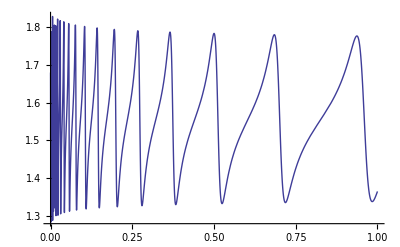

```mathematica
Plot[Abs@zets[n,.51+10I],{n,1,100000000000}]
```

```mathematica
Expand[1/(1-s/(1-s)n^(1-2s)) j^-s - 1/((1-s)/s n^(2s-1)-1) j^(s-1)]
```

-j^(-1+s)/(-1+(n^(-1+2 s) (1-s))/s)+j^-s/(1-(n^(1-2 s) s)/(1-s))

```mathematica
bb[n_,t_,t2_] := {(2t Cos[t Log[n]]-Sin[t Log[n]])Zeta[t2], (2t Sin[t Log[n]]+Cos[t Log[n]])Sum[ j^(-1/2)Sin[t Log[j]],{j,1,n}]+(2t Cos[t Log[n]]-Sin[t Log[n]])Sum[ j^(-1/2)Cos[t Log[j]],{j,1,n}]}
```

```mathematica
bb[100000,.3I+2,.8+2I]
```

{5.37521+39.8772 ⅈ,-34.0654+21.4869 ⅈ}

```mathematica
bc[n_,t_,t2_]:={Zeta[t2],(2 t Sin[t Log[n]] +Cos[t  Log[n]])/(2 t  Cos[t  Log[n]] -Sin[t  Log[n]])Sum[j^(-1/2)Sin[t Log[j]],{j,1,n}]+Sum[j^(-1/2)Cos[t Log[j]],{j,1,n}]}
bc2[n_,t_,t2_]:={Zeta[t2],(2 t Sinh[t Log[n]] +Cosh[t  Log[n]])/(2 t  Cosh[t  Log[n]] -Sinh[t  Log[n]])Sum[j^(-1/2)Sinh[t Log[j]],{j,1,n}]+Sum[j^(-1/2)Cosh[t Log[j]],{j,1,n}]}
ssosub4[n_,s_]:=((1-s)n^s)/((1-s)n^s-s n^(1-s))HarmonicNumber[n,s]
sso10d[n_,s_]:=ssosub4[n,s]+ssosub4[n,1-s]
sso10d10[n_,s_]:=Sum[j^(-1/2)(2 s Cosh[s Log[n/j]] -Sinh[s Log[n/j]])/(2 s Cosh[s Log[n]] -Sinh[s Log[n]]),{j,1,n}]
```

```mathematica
(* Imaginary part is conjugate here.  What am I doing wrong? *)
```

```mathematica
bc2[100000,.3+2I,.8+2I]
```

{0.533102-0.342462 ⅈ,-4297.91+1834.17 ⅈ}

```mathematica
sso10d10[100000,.3+2I]
```

0.533592-0.342803 ⅈ

```mathematica
sso10d11[n_,s_]:=Sum[j^(-1/2)(2 s Cos[s Log[n/j]] -Sin[s Log[n/j]])/(2 s Cos[s Log[n]] -Sin[s Log[n]]),{j,1,n}]
```

```mathematica
sso10d11[100000,.3I+2]
```

0.533592+0.342803 ⅈ

```mathematica
Zeta[.8+2I]
```

0.533102-0.342462 ⅈ

```mathematica
(.3I+2 )I
```

-0.3+2. ⅈ

```mathematica
pr[n_,x_]:= ((2x Sin[x Log[n]]+Cos[x Log[n]])/(2x Cos[x Log[n]]-Sin[x Log[n]]))Sum[ j^(-1/2)Sin[ x Log[j]],{j,1,n}]+Sum[ j^(-1/2)Cos[ x Log[j]],{j,1,n}]
pro[n_,x_]:= ((2x Sin[x Log[n]]+Cos[x Log[n]]))Sum[ j^(-1/2)Sin[ x Log[j]],{j,1,n}]+(2x Cos[x Log[n]]-Sin[x Log[n]])Sum[ j^(-1/2)Cos[ x Log[j]],{j,1,n}]
pra[n_,x_]:= {((2x Sin[x Log[n]]+Cos[x Log[n]])/(2x Cos[x Log[n]]-Sin[x Log[n]])),Sum[ j^(-1/2)Sin[ x Log[j]],{j,1,n}],Sum[ j^(-1/2)Cos[ x Log[j]],{j,1,n}]}
prb[n_,x_]:= ((2x Sin[x Log[n]]+Cos[x Log[n]])/(2x Cos[x Log[n]]-Sin[x Log[n]]))
prs[n_,x_]:= ((2x Sin[x Log[n]]+Cos[x Log[n]]))
prc[n_,x_]:= ((2x Cos[x Log[n]]-Sin[x Log[n]]))
```

```mathematica
sso10d10[n_,s_]:=Sum[j^(-1/2)(2 s Cosh[s Log[n/j]] -Sinh[s Log[n/j]])/(2 s Cosh[s Log[n]] -Sinh[s Log[n]]),{j,1,n}]
sso10d10a[n_,s_]:=Sum[j^(-1/2)(2 s (Cosh[s Log[n]-s Log[j]]) -(Sinh[s Log[n]-s Log[j]]))/(2 s Cosh[s Log[n]] -Sinh[s Log[n]]),{j,1,n}]
sso10d10b[n_,s_]:=Sum[j^(-1/2)(2 s (Cosh[s Log[n]]Cosh[s Log[j]]-Sinh[s Log[n]]Sinh[s Log[j]]) -(Sinh[s Log[n]]Cosh[s Log[j]]-Cosh[s Log[n]]Sinh[s Log[j]]))/(2 s Cosh[s Log[n]] -Sinh[s Log[n]]),{j,1,n}]
sso10d10c[n_,s_]:=Sum[j^(-1/2)(
2 s (Cosh[s Log[n]]Cosh[s Log[j]]-Sinh[s Log[n]]Sinh[s Log[j]]) -
(Sinh[s Log[n]]Cosh[s Log[j]]-Cosh[s Log[n]]Sinh[s Log[j]])
)/(2 s Cosh[s Log[n]] -Sinh[s Log[n]]),{j,1,n}]
sso10d10d[n_,s_]:=(
Sum[j^(-1/2)(2 s (Cosh[s Log[n]]Cosh[s Log[j]])),{j,1,n}]+
Sum[j^(-1/2)(2 s (-Sinh[s Log[n]]Sinh[s Log[j]]) ),{j,1,n}]+
Sum[j^(-1/2)(-(Sinh[s Log[n]]Cosh[s Log[j]])),{j,1,n}]+
Sum[j^(-1/2)(-(-Cosh[s Log[n]]Sinh[s Log[j]])),{j,1,n}]
)/(2 s Cosh[s Log[n]] -Sinh[s Log[n]])
sso10d10e[n_,s_]:=(
(2 s Cosh[s Log[n]]-Sinh[s Log[n]]) Sum[j^(-1/2)Cosh[s Log[j]],{j,1,n}]+
(-2 s Sinh[s Log[n]]+Cosh[s Log[n]]) Sum[j^(-1/2)Sinh[s Log[j]],{j,1,n}]
)/(2 s Cosh[s Log[n]] -Sinh[s Log[n]])
sso10d10f[n_,s_]:=Sum[j^(-1/2)Cosh[s Log[j]],{j,1,n}]-(2 s Sinh[s Log[n]]-Cosh[s Log[n]])/(2 s Cosh[s Log[n]] -Sinh[s Log[n]]) Sum[j^(-1/2)Sinh[s Log[j]],{j,1,n}]
hyp[n_,s_]:=sso10d10f[n,s-1/2]
```

```mathematica
sso10d10f[10000,.3+2I]
```

0.532091-0.340213 ⅈ

```mathematica
Zeta[.8+2I]
```

0.533102-0.342462 ⅈ

```mathematica
hyp[100000,.8+2I]
```

0.533592-0.342803 ⅈ

```mathematica
FullSimplify[(-s a +1/2 b)/(s b -1/2 a )]
```

-(b-2 a s)/(a-2 b s)

```mathematica
Sinh[I x]
```

ⅈ Sin[x]

```mathematica
Cosh[I x]
```

Cos[x]

```mathematica
zetx[n_,t_]:=(t Sin[t Log[n]] +Cos[t  Log[n]]/2)/( t  Cos[t  Log[n]] -Sin[t  Log[n]]/2)Sum[j^(-1/2)Sin[t Log[j]],{j,1,n}]+Sum[j^(-1/2)Cos[t Log[j]],{j,1,n}]
zetj[n_,t_,j_]:=(t Sin[t Log[n]] +Cos[t  Log[n]]/2)/( t  Cos[t  Log[n]] -Sin[t  Log[n]]/2)j^(-1/2)Sin[t Log[j]]+j^(-1/2)Cos[t Log[j]]
```

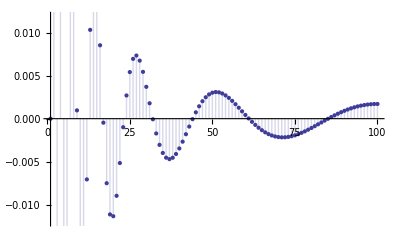

```mathematica
DiscretePlot[Im@ zetj[100,10+1.I,j],{j,1,100}]
```

```mathematica
Zeta[2.5]
```

1.34149